```mathematica
ClearAll["Global`*"]
SubValues[Derivative]={};
```

```mathematica
(* Problem 1 *)

(* Energies *)
T=(1/2) m (y'[t]^2+z'[t]^2) ;
V=m g z[t];

(* Geometric contrainsts *)
y[t_] = l Sin[θ[t]];

z[t_] = l Cos[θ[t]];

T=Collect[T,θ,Simplify]
V=Simplify[V]
L = T-V;
```

1/2 l^2 m (θ'(t))^2

g l m cos(θ(t))

```mathematica
(* E-L equations *)
eqn1=Simplify[D[D[L,θ'[t]],t]-D[L,θ[t]]]- τ
θtt=Solve[eqn1==0,θ''[t]][[1,1,2]]
```

l m (l θ''(t)-g sin(θ(t)))-τ

(g l m sin(θ(t))+τ)/(l^2 m)

```mathematica
leqn1 = eqn1 /. {Sin[θ[t]]->θ[t]}
```

l m (l θ''(t)-g θ(t))-τ

```mathematica
Collect[leqn1,{θ''[t],θ[t]}]
```

-g l m θ(t)+l^2 m θ''(t)-τ

```mathematica
(* Solve for state space equations *)
sol = Solve[leqn1==0,θ''[t]];
p1 = Collect[sol[[1,1]],θ[t]]
a11 = p1[[2,2]]/.θ[t]->1
b1 = p1[[2,1]] /. τ->1
```

θ''(t)→(g θ(t))/l+τ/(l^2 m)

g/l

1/(l^2 m)

```mathematica
(* State space matrix *)
A= {{0,1},
{a11,0}} 
B = {{0},{b1}}
```

(0 | 1
g/l | 0)

(0
1/(l^2 m))

```mathematica
Q = Transpose[{B, A.B} ]
```

({0} | {1/(l^2 m)}
{1/(l^2 m)} | {0})

```mathematica
B
```

(0
1/(l^2 m))

```mathematica
A.B
```

(1/(l^2 m)
0)

```mathematica
Q = {{0,1/(l^2 m)},{1/(l^2 m),0}}
```

(0 | 1/(l^2 m)
1/(l^2 m) | 0)

```mathematica
(* Matrix Rank of Q = N, so the system is controllable*)
MatrixRank[Q]
```

2

```mathematica
T1 = {0,1}.Inverse[Q]
{{T1},{T1.A}}
```

{l^2 m,0}

({l^2 m,0}
{0,l^2 m})

```mathematica
T = {{l^2 m,0},{0,l^2 m}}
```

(l^2 m | 0
0 | l^2 m)

```mathematica
A1 = T.A.Inverse[T]
B1 = T.B
```

(0 | 1
g/l | 0)

(0
1)

```mathematica
Clear[gz,bg];
Gz=Array[gz,2];
B1Gz=Array[bg,{2,2}];
Do[bg[i,j]=B1[[i]] gz[j],{i,1,2},{j,1,2}];
B1Gz
```

({0} | {0}
{gz(1)} | {gz(2)})

```mathematica
B1Gz = {{0,0},{gz[1],gz[2]}}
```

(0 | 0
gz(1) | gz(2))

```mathematica
A1star=A1-B1Gz
```

(0 | 1
g/l-gz(1) | -gz(2))

```mathematica
M1star=s IdentityMatrix[2]-A1star;
cpz=Collect[Det[M1star],s,Simplify]
```

-g/l+gz(2) s+gz(1)+s^2

```mathematica
cp0=Collect[(s-s1) (s-s2),s,Simplify]
```

s^2+s (-s1-s2)+s1 s2

```mathematica
g1=Coefficient[cpz,s,1]-Coefficient[cp0,s,1]
g2=Coefficient[cpz,s,0]-Coefficient[cp0,s,0]
```

gz(2)+s1+s2

-g/l+gz(1)-s1 s2

```mathematica
Clear[gz,s1,s2];
Solve[{g1==0,g2==0},{gz[1],gz[2]}];
{gz[1],gz[2]}={gz[1],gz[2]}/.%[[1]];
zgains={gz[1],gz[2]}
```

{(g+l s1 s2)/l,-s1-s2}

```mathematica
{s1,s2}=Eigenvalues[A];
Chop[zgains]
```

{0,0}

```mathematica
Clear[s1,s2]
zgains
xgains=(zgains.T)
```

{(g+l s1 s2)/l,-s1-s2}

{l m (g+l s1 s2),l^2 m (-s1-s2)}

```mathematica
{s1,s2}={-1,-1}
```

{-1,-1}

```mathematica
zgains
xgains
```

{(g+l)/l,2}

{l m (g+l),2 l^2 m}

```mathematica
(* Choose state vector = {θ, θt}
```

```mathematica
X = Array[x,2]
x1t = x[2];
x2t=θtt;
θ=x[1]; θ'[t] =x[2];
xt = {x1t,x2t}
```

{x(1),x(2)}

{x(2),(g l m sin(x(1)(t))+τ)/(l^2 m)}

```mathematica
xdot = xt /.{x[2]->x2[t],x[1][t]->x1[t]}
```

{x2(t),(g l m sin(x1(t))+τ)/(l^2 m)}

```mathematica
ode1=x1'[t]==xdot[[1]]
ode2=x2'[t]==xdot[[2]]
```

x1'(t)==x2(t)

x2'(t)==(g l m sin(x1(t))+τ)/(l^2 m)

```mathematica
parameters = {l->1,m->1, τ->0, g->9.81}
nodes = {ode1 /. parameters,ode2 /. parameters}
```

{l→1,m→1,τ→0,g→9.81}

{x1'(t)==x2(t),x2'(t)==9.81 sin(x1(t))}

```mathematica
ics={x1[0]==θ0, x2[0]==ω0}
```

{x1(0)==θ0,x2(0)==ω0}

```mathematica
ans={x1[t],x2[t]}
```

{x1(t),x2(t)}

```mathematica
nodes
```

{x1'(t)==x2(t),x2'(t)==g sin(x1(t))}

InterpolatingFunction[(0. | 100.),<>](t)

InterpolatingFunction[(0. | 100.),<>](t)

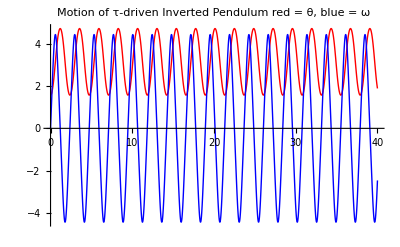

```mathematica
θ0=π/2;
ω0=0;
tf = 100;
soln=NDSolve[{nodes,ics},ans,{t,0,tf}];
nθ=soln[[1,1,2]];
nω=soln[[1,2,2]];
NonlinearPicture = Plot[{nθ,nω},{t,0,40}, PlotStyle->{Red,Blue},PlotLabel->"Motion of τ-driven Inverted Pendulum\nred = θ, blue = ω",
PlotRange->All]
Clear[θ0,ω0];
```

```mathematica
Save["Problem4Sim",{nodes,ics,ans}];
```